### Start choosing the example:

```mathematica
t=10;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,0,1},{0,1,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1},{3,I2}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{{1,2,4,S1},{1,2,3,S2},{3,2,1,S3},{3,2,4,S4},{4,2,1,S5},{4,2,3,S6}}|>

```mathematica
sc=Data["Switching Costs"]
```

{{1,2,4,S1},{1,2,3,S2},{3,2,1,S3},{3,2,4,S4},{4,2,1,S5},{4,2,3,S6}}

```mathematica
ConsistentSwithingCosts[Data][{a_,b_,c_,S_}]:=
Module[{sc = Data["Switching Costs"],or, de, bounds},
or=Cases[sc,{a,b,_,_}];
de=Cases[sc,{_,b,c,_}];
bounds=Outer[Plus,Last/@or,Last/@de]//Flatten;
And @@ (S≤ # &)/@bounds
]
```

```mathematica
And@@ConsistentSwithingCosts[Data]/@sc
```

S1≤2 S1&&S1≤S1+S4&&S1≤S1+S2&&S1≤S2+S4&&S2≤S1+S2&&S2≤S1+S6&&S2≤2 S2&&S2≤S2+S6&&S3≤2 S3&&S3≤S3+S5&&S3≤S3+S4&&S3≤S4+S5&&S4≤S1+S3&&S4≤S3+S4&&S4≤S1+S4&&S4≤2 S4&&S5≤S3+S5&&S5≤2 S5&&S5≤S3+S6&&S5≤S5+S6&&S6≤S2+S5&&S6≤S5+S6&&S6≤S2+S6&&S6≤2 S6

```mathematica
Outer[Plus,Last/@or,Last/@de]//Flatten
```

{2 S1,S1+S4,S1+S2,S2+S4}

```mathematica
(*1,2,4*)
or=Cases[sc, {1,2,_,_}]
```

{{1,2,4,S1},{1,2,3,S2}}

```mathematica
de=Cases[sc, {_,2,4,_}]
```

{{1,2,4,S1},{3,2,4,S4}}

```mathematica
MFGEquations=DataToEquations[Data];//Timing
MFGEquations["criticalreduced1"][[2]]//KeySort
```

AdjacencyGraph::matsq: Argument Missing[KeyAbsent,29] at position 2 is not a non-empty square matrix.

First::normal: Nonatomic expression expected at position 1 in First[KeyAbsent].

First::normal: Nonatomic expression expected at position 1 in First[29].

MapThread::mptd: Object Missing[Missing[KeyAbsent,First[KeyAbsent]],Missing[KeyAbsent,First[29]]] at position {2, 1} in MapThread[DirectedEdge,{Missing[Missing[KeyAbsent,First[KeyAbsent]],«1»],Missing[First[KeyAbsent],«1»]}] has only 0 of required 1 dimensions.

First::normal: Nonatomic expression expected at position 1 in First[KeyAbsent].

General::stop: Further output of First::normal will be suppressed during this calculation.

MapThread::mptd: Object Missing[First[KeyAbsent],First[29]] at position {2, 1} in MapThread[DirectedEdge,{Missing[First[KeyAbsent],First[29]],Missing[Missing[«1»],Missing[Ke…nt,«1»]]}] has only 0 of required 1 dimensions.

MapThread::argt: MapThread called with 4 arguments; 2 or 3 arguments are expected.

EdgeAdd::graph: A graph object is expected at position 1 in EdgeAdd[AdjacencyGraph[Missing[KeyAbsent,29],Missing[KeyAbsent,29],VertexLabels→Name],MapThread[«1»]].

EdgeList::graph: A graph object is expected at position 1 in EdgeList[EdgeAdd[AdjacencyGraph[Missing[KeyAbsent,29],Missing[KeyAbsent,29],VertexLabels→Name],«1»]].

EdgeList::graph: A graph object is expected at position 1 in EdgeList[AdjacencyGraph[Missing[KeyAbsent,29],Missing[KeyAbsent,29],VertexLabels→Name]].

EdgeList::graph: A graph object is expected at position 1 in EdgeList[AtHead[EdgeAdd[AdjacencyGraph[Missing[KeyAbsent,29],Missing[KeyAbsent,29],VertexLabels→Name],«1»]]].

General::stop: Further output of EdgeList::graph will be suppressed during this calculation.

VertexList::graph: A graph object is expected at position 1 in VertexList[EdgeAdd[AdjacencyGraph[Missing[KeyAbsent,29],Missing[KeyAbsent,29],VertexLabels→Name],«1»]].

IncidenceList::graph: A graph object is expected at position 1 in IncidenceList[EdgeAdd[AdjacencyGraph[Missing[KeyAbsent,29],Missing[KeyAbsent,29],VertexLabels→Name],«1»],«1»].

IncidenceList::graph: A graph object is expected at position 1 in IncidenceList[EdgeAdd[AdjacencyGraph[Missing[KeyAbsent,29],Missing[KeyAbsent,29],VertexLabels→Name],«1»],«1»,«1»].

General::stop: Further output of IncidenceList::graph will be suppressed during this calculation.

VertexList::graph: A graph object is expected at position 1 in VertexList[{«1»}].

Last::normal: Nonatomic expression expected at position 1 in Last[KeyAbsent].

Last::normal: Nonatomic expression expected at position 1 in Last[29].

MapThread::list: List expected at position 2 in MapThread[AtHead[DirectedEdge],AtHead[{Missing[Missing[KeyAbsent,First[KeyAbsent]],Missing[«1»]],«1»}]].

MapThread::list: List expected at position 2 in MapThread[True,True].

MapThread::list: List expected at position 2 in MapThread[AtHead[DirectedEdge],AtHead[{Missing[Missing[KeyAbsent,First[KeyAbsent]],Missing[«1»]],«1»}]].

General::stop: Further output of MapThread::list will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[KeyAbsent].

General::stop: Further output of Last::normal will be suppressed during this calculation.

Take::normal: Nonatomic expression expected at position 1 in Take[KeyAbsent,3].

Take::normal: Nonatomic expression expected at position 1 in Take[29,3].

Join::heads: Heads Catenate and Missing at positions 1 and 2 are expected to be the same.

Join::heads: Heads List and Missing at positions 1 and 2 are expected to be the same.

Outer::heads: Heads EdgeList and MapThread at positions 3 and 2 are expected to be the same.

Outer::heads: Heads MapThread and Missing at positions 3 and 2 are expected to be the same.

Join::heads: Heads List and ToRules at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

ReplaceAll::reps: {Join[{},ToRules[MFGraphs`Private`ExitValues[Graph[MapThread[DirectedEdge,{«2»},«12»,{«2»}],«12»→«6»]]&&«1»]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted

Part::partw: Part 2 of MFGEquations[criticalreduced1] does not exist.

KeySort::invrl: The argument MFGEquations[criticalreduced1]⟦2⟧ is not a valid Association or a list of rules.

KeySort[MFGEquations[criticalreduced1]⟦2⟧]

```mathematica
Values[%]
```

{0,2,0,0,2,2,0,0,0,0,2,0,0,0,0,0,2,0,0,0,5,5,7,9,7,7,5,7,9,7}

```mathematica
Values@KeySort@nsol2
```

{0,2,0,0,2,2,0,0,0,0,2,0,0,0,0,0,2,0,0,0,5,5,7,9,7,7,5,7,9,7}

#### Non-linear case

```mathematica
Data=DataG[t];
MFGEquations=DataToEquations[Data];
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

Eliminator: System is not True and Head of system is NOT And or Equal. Returning the input.

DataToEquations: Critical case ...

Eliminator: System is not True and Head of system is NOT And or Equal. Returning the input.

EqEliminatorX: Reached a solution!

DataToEquations: Done.

```mathematica
nsol1=FixedPoint[FixedSolverStepX1[MFGEquations], MFGEquations["criticalreduced"][[2]],6, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)]
```

Step: nonlinear: -j514-u529+u534==0&&2-j514-u531+u536==0

EqEliminatorX: Reached a solution!

<|j513→2,u535→5,u537→9,j509→0,j510→2,j511→2-2,j512→2-2,j515→0,j516→0,j517→0,j518→0,jt519→2,jt520→0,jt521→0,jt522→0,jt523→0,jt524→0,jt525→2,jt526→2-2,jt527→2-2,jt528→0,u530→5,u532→9,u538→7,u534→2+5,u536→-2+2+7,j514→2,u529→5,u531→7,u533→7|>

```mathematica
Values[nsol1//KeySort]
```

{0,2,0,0,2,2,0,0,0,0,2,0,0,0,0,0,2,0,0,0,5,5,7,9,7,7,5,7,9,7}

```mathematica
nsol2=FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced"][[2]],6, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)]
```

Step: nonlinear: -j514-u529+u534==0&&2-j514-u531+u536==0

System Heads: {NonNegative,Equal,Or}

Rules association input: <|j513→2,u535→5,u537→9,j509→0,j510→j514,j511→2-j514,j512→2-j514,j515→0,j516→0,j517→0,j518→0,jt519→j514,jt520→0,jt521→0,jt522→0,jt523→0,jt524→0,jt525→j514,jt526→2-j514,jt527→2-j514,jt528→0,u530→5,u532→9,u538→u533|>

NonNegative: NonNegative[j514]&&NonNegative[2-j514]&&NonNegative[2-j514]&&NonNegative[j514]&&NonNegative[j514]&&NonNegative[j514]&&NonNegative[2-j514]&&NonNegative[2-j514]&&NonNegative[5-u529]&&NonNegative[-u531+u534]&&NonNegative[-u533+u534]&&NonNegative[u531-u534]&&NonNegative[u531-u533]&&NonNegative[9-u536]

Alternatives: (j514==0||-5+u529==0)&&(j514==0||u533-u534==0)&&(2-j514==0||-u531+u533==0)&&(2-j514==0||-9+u536==0)

Equalities: -j514-u529+u534==0&&2-j514-u531+u536==0

<|j513→2,u535→5,u537→9,j509→0,j510→j514,j511→2-j514,j512→2-j514,j515→0,j516→0,j517→0,j518→0,jt519→j514,jt520→0,jt521→0,jt522→0,jt523→0,jt524→0,jt525→j514,jt526→2-j514,jt527→2-j514,jt528→0,u530→5,u532→9,u538→u533,u534→j514+u529,u536→-2+j514+u531|>

<|j513→2,u535→5,u537→9,j509→0,j510→2,j511→2-2,j512→2-2,j515→0,j516→0,j517→0,j518→0,jt519→2,jt520→0,jt521→0,jt522→0,jt523→0,jt524→0,jt525→2,jt526→2-2,jt527→2-2,jt528→0,u530→5,u532→9,u538→7,u534→2+5,u536→-2+2+7,j514→2,u529→5,u531→7,u533→7|>

```mathematica
Values@KeySort@nsol2
```

{0,2,0,0,2,2,0,0,0,0,2,0,0,0,0,0,2,0,0,0,5,5,7,9,7,7,5,7,9,7}

```mathematica
(MFGEquations["Nlhs"])/.nsol
MFGEquations["Nrhs"]/.nsol
```

{17.2731,0.}

{0.,-17.2731}

```mathematica
MFGEquations["Nlhs"]/.MFGEquations["criticalreduced"][[2]]
MFGEquations["Nrhs"]/.MFGEquations["criticalreduced"][[2]]
```

{0,0}

{17.2731,0.}

```mathematica
MFGEquations["Nrhs"]
```

{-j229+Intg[-j229],2-j229+Intg[2-j229]}

```mathematica
Norm[(MFGEquations["Nrhs"]-MFGEquations["Nlhs"])/.nsol]
```

24.4279

```mathematica
FixedSolverStepX2[MFGEquations][MFGEquations["criticalreduced"][[2]]]//KeySort
```

System Heads: {NonNegative,Equal,Or}

Rules association input: <|j228→2,u250→1,u252→5,j224→0,j225→j229,j226→2-j229,j227→2-j229,j230→0,j231→0,j232→0,j233→0,jt234→j229,jt235→0,jt236→0,jt237→0,jt238→0,jt239→0,jt240→j229,jt241→2-j229,jt242→2-j229,jt243→0,u245→1,u247→5,u253→u248|>

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

<|j224→0,j225→0,j226→2-0,j227→2-0,j228→2,j229→0,j230→0,j231→0,j232→0,j233→0,jt234→0,jt235→0,jt236→0,jt237→0,jt238→0,jt239→0,jt240→0,jt241→2-0,jt242→2-0,jt243→0,u244→-10.2731,u245→1,u246→7.,u247→5,u248→7.,u249→17.2731+1. 0+1. (-10.2731),u250→1,u251→-2.+1. 0+1. 7.,u252→5,u253→7.|>

### What we this plot for?

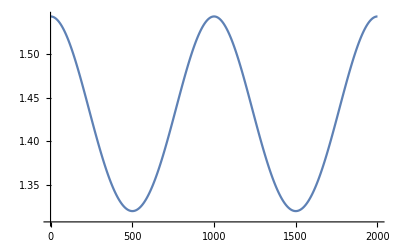

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.

### New alternative to solving the equations

```mathematica
AA=MFGEquations["EqAllAll"];
NN=Select[AA,Head[#]===NonNegative&];
OO = Select[AA,Head[#]===Or&];
EE=Select[AA,Head[#]===Equal&];
Timing[Simplify[NN];](*note the semi-colon!*)
Timing[FullSimplify[NN];]
Timing[Reduce[NN,Reals];](*Takes more time, but shows the equalities.*)
```

{0.000161,Null}

{0.000099,Null}

{0.009054,Null}

### One iteration to solve the critical congestion case:

```mathematica
rdcd=EqEliminatorX2[{MFGEquations["EqAllAll"]&&MFGEquations["EqCriticalCase"], MFGEquations["BoundaryRules"]}]
```

```mathematica
rdcd=FixedPoint[EqEliminatorX2,{MFGEquations["EqAllAll"], MFGEquations["BoundaryRules"]},10]
```

{(j15==0||-2+u45==0)&&(2-j15==0||-1+u46==0),NonNegative[j15]&&NonNegative[2-j15]&&NonNegative[j15]&&NonNegative[2-j15]&&NonNegative[j15]&&NonNegative[2-j15]&&NonNegative[j15]&&NonNegative[2-j15]&&NonNegative[2-u45]&&NonNegative[1-u46],<|j19→2,u47→2,u48→1,j14→2,j16→2-j15,j17→j15,j18→2-j15,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→2,jt28→j15+0,jt29→2-j15-0,jt30→-0,jt31→0,jt33→-0,jt34→j15,jt35→0,jt36→2-j15,jt37→0,u41→2,u42→1,u49→u38,jt32→0,u39→u40,u43→u38,u44→u40|>}

```mathematica
rdcd[[1]] = rdcd[[1]]&&rdcd[[2]]
```

(j15==0||-2+u45==0)&&(2-j15==0||-1+u46==0)&&NonNegative[j15]&&NonNegative[2-j15]&&NonNegative[j15]&&NonNegative[2-j15]&&NonNegative[j15]&&NonNegative[2-j15]&&NonNegative[j15]&&NonNegative[2-j15]&&NonNegative[2-u45]&&NonNegative[1-u46]

```mathematica
rdcd[[2]] =rdcd[[3]]
```

<|j19→2,u47→2,u48→1,j14→2,j16→2-j15,j17→j15,j18→2-j15,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→2,jt28→j15+0,jt29→2-j15-0,jt30→-0,jt31→0,jt33→-0,jt34→j15,jt35→0,jt36→2-j15,jt37→0,u41→2,u42→1,u49→u38,jt32→0,u39→u40,u43→u38,u44→u40|>

```mathematica
rdcd
```

{(j15==0||-2+u45==0)&&(2-j15==0||-1+u46==0)&&NonNegative[j15]&&NonNegative[2-j15]&&NonNegative[j15]&&NonNegative[2-j15]&&NonNegative[j15]&&NonNegative[2-j15]&&NonNegative[j15]&&NonNegative[2-j15]&&NonNegative[2-u45]&&NonNegative[1-u46],<|j19→2,u47→2,u48→1,j14→2,j16→2-j15,j17→j15,j18→2-j15,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→2,jt28→j15+0,jt29→2-j15-0,jt30→-0,jt31→0,jt33→-0,jt34→j15,jt35→0,jt36→2-j15,jt37→0,u41→2,u42→1,u49→u38,jt32→0,u39→u40,u43→u38,u44→u40|>,<|j19→2,u47→2,u48→1,j14→2,j16→2-j15,j17→j15,j18→2-j15,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→2,jt28→j15+0,jt29→2-j15-0,jt30→-0,jt31→0,jt33→-0,jt34→j15,jt35→0,jt36→2-j15,jt37→0,u41→2,u42→1,u49→u38,jt32→0,u39→u40,u43→u38,u44→u40|>}

```mathematica
EqEliminatorX2[rdcd]
```

System Heads: Equal

Rules association input: <|j195→2,u217→1,u219→5,j191→0,j192→j196,j193→2-j196,j194→2-j196,j197→0,j198→0,j199→0,j200→0,jt201→j196,jt202→0,jt203→0,jt204→0,jt205→0,jt206→0,jt207→j196,jt208→2-j196,jt209→2-j196,jt210→0,u212→1,u214→5,u216→j196+u211,u218→-2+j196+u213,u220→u215|>

{True,True,<|j195→2,u217→1,u219→5,j191→0,j192→2,j193→2-2,j194→2-2,j197→0,j198→0,j199→0,j200→0,jt201→2,jt202→0,jt203→0,jt204→0,jt205→0,jt206→0,jt207→2,jt208→2-2,jt209→2-2,jt210→0,u212→1,u214→5,u216→2+1,u218→-2+2+3,u220→3,j196→2,u211→1,u213→3,u215→3|>}

```mathematica
m=4;rdcd2=FixedPointList[EqEliminatorX2,rdcd,m]
```

```mathematica
EqEliminatorX2[{MFGEquations["reduced"][[1]]&&MFGEquations["EqCriticalCase"], MFGEquations["reduced"][[2]]}]
```

{(u344<5&&u337==1&&j322==2&&u341==u342&&u339==u342)||(u344==5&&((u337<1&&j322==0&&u341==u342&&u339==u342)||(u337==1&&0≤j322≤2&&u341==u342&&u339==u342))),True,-j322-u337+u342==0&&2-j322-u339+u344==0,<|j321→2,u343→1,u345→5,j317→0,j318→j322,j319→2-j322,j320→2-j322,j323→0,j324→0,j325→0,j326→0,jt327→j322,jt328→0,jt329→0,jt330→0,jt331→0,jt332→0,jt333→j322,jt334→2-j322,jt335→2-j322,jt336→0,u338→1,u340→5,u346→u341,u342→j322+u337,u344→-2+j322+u339|>}

```mathematica
Reduce[And @@(FullSimplify[rdcd[[2]]/.rdcd[[4]]][[#]]&/@Range[3]),Reals]
```

0≤j256≤2&&u271≤1

```mathematica
rdcd2
```

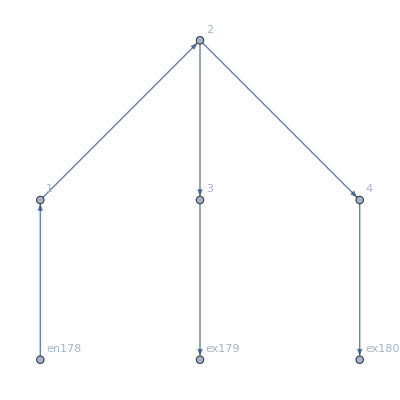
<|FG→-Graphics-,EqAllAll→NonNegative[j181]&&NonNegative[j182]&&NonNegative[j183]&&NonNegative[j184]&&NonNegative[j185]&&NonNegative[j186]&&NonNegative[j187]&&NonNegative[j188]&&NonNegative[j189]&&NonNegative[j190]&&NonNegative[j191]&&NonNegative[j192]&&NonNegative[jt193]&&NonNegative[jt194]&&NonNegative[jt195]&&NonNegative[jt196]&&NonNegative[jt197]&&NonNegative[jt198]&&NonNegative[jt199]&&NonNegative[jt200]&&NonNegative[jt201]&&NonNegative[jt202]&&NonNegative[jt203]&&NonNegative[jt204]&&j187==jt193&&j186==jt194&&j181==jt195+jt196&&j188==jt197+jt198&&j189==jt199+jt200&&j182==jt201&&j190==jt202&&j183==jt203&&j191==jt204&&j181==jt194&&j192==jt193&&j187==jt197+jt199&&j182==jt195+jt200&&j183==jt196+jt198&&j188==jt202&&j184==jt201&&j189==jt204&&j185==jt203&&j186==2&&u214==2&&u215==1&&NonNegative[u205-u216]&&NonNegative[-u206+u211]&&NonNegative[-u207+u211]&&NonNegative[u206-u211]&&NonNegative[u206-u207]&&NonNegative[u207-u211]&&NonNegative[-u206+u207]&&NonNegative[u208-u212]&&NonNegative[u209-u213]&&-u210+u216==0&&-u208+u214==0&&-u209+u215==0&&(j187==0||j181==0)&&(j188==0||j182==0)&&(j189==0||j183==0)&&(j190==0||j184==0)&&(j191==0||j185==0)&&(j192==0||j186==0)&&(jt193==0||jt194==0)&&(jt195==0||jt197==0)&&(jt196==0||jt199==0)&&(jt198==0||jt200==0)&&(jt201==0||jt202==0)&&(jt203==0||jt204==0)&&jt193==0&&(jt194==0||-u205+u216==0)&&(jt195==0||-u206+u211==0)&&(jt196==0||-u207+u211==0)&&(jt197==0||u206-u211==0)&&(jt198==0||u206-u207==0)&&(jt199==0||u207-u211==0)&&(jt200==0||-u206+u207==0)&&(jt201==0||-u208+u212==0)&&jt202==0&&(jt203==0||-u209+u213==0)&&jt204==0,BoundaryRules→{j186→2,u214→2,u215→1},reduced→{(u213<1&&u212==2&&j182==2&&u207==u211&&u206==u211&&jt199==0)||(u213==1&&((u212<2&&j182==0&&u207==u211&&u206==u211&&jt199==0)||(u212==2&&0≤j182≤2&&u207==u211&&u206==u211&&jt199==0))),<|j186→2,u214→2,u215→1,j181→2,j183→2-j182,j184→j182,j185→2-j182,j187→0,j188→0,j189→0,j190→0,j191→0,j192→0,jt193→0,jt194→2,jt195→j182+jt199,jt196→2-j182-jt199,jt197→-jt199,jt198→jt199,jt200→-jt199,jt201→j182,jt202→0,jt203→2-j182,jt204→0,u208→2,u209→1,u216→u205,u210→u205|>},Nlhs→{2-u205+u211,j182-u206+u212,2-j182-u207+u213},EqCriticalCase→2-u205+u211==0&&j182-u206+u212==0&&2-j182-u207+u213==0,criticalreduced→{True,<|j186→2,u214→2,u215→1,j181→2,j183→2-1/2,j184→1/2,j185→2-1/2,j187→0,j188→0,j189→0,j190→0,j191→0,j192→0,jt193→0,jt194→2,jt195→1/2+0,jt196→2-1/2-0,jt197→-0,jt198→0,jt200→-0,jt201→1/2,jt202→0,jt203→2-1/2,jt204→0,u208→2,u209→1,u216→9/2,u210→9/2,u211→-2+9/2,u212→-1/2+5/2,u213→-2+1/2+5/2,j182→1/2,jt199→0,u205→9/2,u206→5/2,u207→5/2|>},Nrhs→{-2.5,j182+Intg[j182],2-j182+Intg[2-j182]},EqGeneralCase→2-u205+u211==-2.5&&j182-u206+u212==j182+Intg[j182]&&2-j182-u207+u213==2-j182+Intg[2-j182]|>

```mathematica
MFGEquations
```

```mathematica
FixedSolverStepX2[MFGEquations][]
```

### ideas

use reduce and compare

```mathematica
use hand results in the solvers and see if they are fixedpoints.
```

```mathematica
make another function to iterate: eliminator + reduce.
```

```mathematica
boolean convert should not be necessary, right? what if solutions are not exact (typical in nonlinear cases)?
```

```mathematica
system= x==y&&(y==3||x==2)&&NonNegative[z]&&(y==2||z==-5)&&(x==2 y || y==2);
```

```mathematica
EqEliminatorX[{system,{}}]
```

{(x==3||x==2)&&NonNegative[z]&&(x==2||z==-5)&&(x==2 x||x==2),<|y→x|>}

```mathematica
EqEliminatorX[%]
```

{(x==3||x==2)&&NonNegative[z]&&(x==2||z==-5)&&(x==2 x||x==2),<|y→x|>}

```mathematica
Reduce[%[[1]]]
```

```mathematica
Solve[x==2&&z≥0]
```

Solve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

{{x→2}}

```mathematica
EqEliminatorX[%]
```

{False,<|x→1,y→3,z→-5|>}

```mathematica
Reduce[x==2&&x>0]
```

x==2